# ImStat

Statistics of image collection

## Setup and data collection

## Config

Source folder for JPG files:

```mathematica
imageDir="/media/superraid/images/images/";
```

Nr of raw files:

```mathematica
nrRawFiles=FileNames["*.CR2",imageDir,∞]//Length
```

9981

```mathematica
jpgFileNames=FileNames["*.jpg"|"*.JPG",imageDir,∞];
```

Number of images found:

```mathematica
nrJpgFiles=Length[jpgFileNames]
```

3955

Folder for local data storage:

```mathematica
dataDir=FileNameJoin[{NotebookDirectory[],"dataStorage"}]
```

/home/malte/dev/imStat/dataStorage

```mathematica
CreateDirectory[dataDir]
```

/home/malte/dev/imStat/dataStorage

## Retrieve mini JPG files and basic data

Compute data file name from original path, making sure that no collisions will occur:

```mathematica
(Union[Hash[#,"CRC32"]&/@jpgFileNames]//Length)==nrJpgFiles
```

True

```mathematica
storageFile[path_]:=FileNameJoin[{dataDir,ToString[Hash[path,"CRC32"]]<>".dst"}];
```

```mathematica
storageFileImg[path_]:=storageFileImg[path]=FileNameJoin[{dataDir,ToString[Hash[path,"CRC32"]]<>".jpg"}];
```

Fetch original image and save data into data file:

```mathematica
createData[path_]/;FileExistsQ[storageFile[path]]=Null;
```

```mathematica
createData[path_]:=Module[{img,dimensions,smallImg,aperture,bitDepth,orientation,colorSpace,date,exposure,focalLength,imageSize,iso,manufacturer,model,exifData},
exifData=Import[path,{{"Aperture","BitDepth","CameraTopOrientation","ColorSpace","Date","Exposure","FocalLength","ImageSize","ISOSpeed","Manufacturer","Model"}}];
If[!MatchQ[exifData,{_,_,_,_String,{_,_,_,_,_,_},_,_,{_,_},_,_String,_String}],
Return[$Failed];
];
img=Import[path];
dimensions=ImageDimensions[img];
smallImg=ImageResize[img,{300},Resampling->"Bilinear"];
Put[{dimensions,exifData},storageFile[path]];
Export[storageFileImg[path],smallImg];
]
```

File size:

```mathematica
fileSizes={#,FileByteCount[#]}&/@jpgFileNames;
```

```mathematica
Put[fileSizes,FileNameJoin[{dataDir,"fileSizes.dst"}]];
```

Retrieving file sizes:

```mathematica
fileSizes=Get[FileNameJoin[{dataDir,"fileSizes.dst"}]];
```

Fetch data in order of preference {memory, data file}:

```mathematica
ClearAll[getData];
getData[path_]/;FileExistsQ[storageFile[path]]:=getData[path]={Import[storageFileImg[path]],Get[storageFile[path]]}
```

```mathematica
getData[_]:=$Failed
```

Accessor functions for properties:

```mathematica
getData[path_,"Date"]:=getData[path][[2,2,5]]
```

```mathematica
getData[path_,"Orientation"]:=getData[path][[2,2,3]]
```

```mathematica
getData[path_,"Camera"]:=getData[path][[2,2,10;;11]]
```

```mathematica
getData[path_,"Aperture"]:=getData[path][[2,2,1]]
```

```mathematica
getData[path_,"BitDepth"]:=getData[path][[2,2,2]]
```

```mathematica
getData[path_,"ColorSpace"]:=getData[path][[2,2,4]]
```

```mathematica
getData[path_,"Exposure"]:=getData[path][[2,2,6]]
```

```mathematica
getData[path_,"FocalLength"]:=getData[path][[2,2,7]]
```

```mathematica
getData[path_,"ImageSize"]:=getData[path][[2,1]]
```

```mathematica
getData[path_,"ISO"]:=getData[path][[2,2,9]]
```

## Retrieve image data

```mathematica
Monitor[
ParallelDo[createData[jpgFileNames[[i]]],{i,Length[jpgFileNames]}],
Refresh[
ProgressIndicator[Length@FileNames["*",dataDir],{0,2Length[jpgFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
]
```

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

```mathematica
goodFileNames=Select[jpgFileNames,FileExistsQ[storageFile[#]]&&FileExistsQ[storageFileImg[#]]&];
```

## Results

## Number of images taken

```mathematica
nrJpg=Length[jpgFileNames]
```

3955

```mathematica
nrGood=Length[goodFileNames]
```

3686

```mathematica
nrNotGood=nrJpg-nrGood
```

269

```mathematica
PieChart[{nrGood,nrNotGood},ChartLabels->{"","No data"}]
```

-Graphics-

## Images taken over time

```mathematica
getData[goodFileNames[[1]],"Date"]
```

{2007,12,23,17,14,56}

```mathematica
imageDates=Monitor[
Table[getData[goodFileNames[[i]],"Date"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
oldestYear=Min@imageDates[[All,1]]
```

2006

```mathematica
newestYear=Max@imageDates[[All,1]]
```

2012

```mathematica
nrTakenTime=Join@@Table[{{y,m},Length@Cases[imageDates,{y,m,d_,h_,mi_,s_}]},{y,oldestYear,newestYear},{m,1,12}]
```

{{{2006,1},0},{{2006,2},0},{{2006,3},0},{{2006,4},0},{{2006,5},0},{{2006,6},0},{{2006,7},0},{{2006,8},0},{{2006,9},0},{{2006,10},0},{{2006,11},0},{{2006,12},6},{{2007,1},0},{{2007,2},8},{{2007,3},22},{{2007,4},138},{{2007,5},44},{{2007,6},42},{{2007,7},90},{{2007,8},41},{{2007,9},244},{{2007,10},170},{{2007,11},114},{{2007,12},166},{{2008,1},286},{{2008,2},202},{{2008,3},261},{{2008,4},91},{{2008,5},253},{{2008,6},190},{{2008,7},233},{{2008,8},429},{{2008,9},0},{{2008,10},2},{{2008,11},1},{{2008,12},26},{{2009,1},2},{{2009,2},3},{{2009,3},0},{{2009,4},20},{{2009,5},3},{{2009,6},5},{{2009,7},8},{{2009,8},0},{{2009,9},0},{{2009,10},6},{{2009,11},0},{{2009,12},2},{{2010,1},0},{{2010,2},0},{{2010,3},0},{{2010,4},0},{{2010,5},3},{{2010,6},0},{{2010,7},1},{{2010,8},1},{{2010,9},0},{{2010,10},7},{{2010,11},6},{{2010,12},1},{{2011,1},151},{{2011,2},0},{{2011,3},0},{{2011,4},249},{{2011,5},10},{{2011,6},9},{{2011,7},1},{{2011,8},0},{{2011,9},3},{{2011,10},35},{{2011,11},0},{{2011,12},0},{{2012,1},0},{{2012,2},0},{{2012,3},60},{{2012,4},8},{{2012,5},0},{{2012,6},33},{{2012,7},0},{{2012,8},0},{{2012,9},0},{{2012,10},0},{{2012,11},0},{{2012,12},0}}

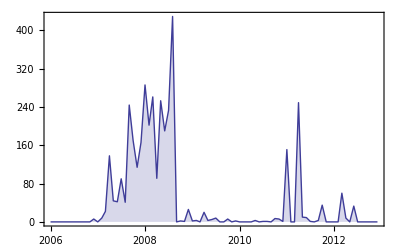

```mathematica
timeTakenPlot=DateListPlot[nrTakenTime,Joined->True,PlotRange->All,Filling->Axis,GridLines->None]
```

## Camera models

```mathematica
getData[goodFileNames[[1]],"Camera"]
```

{Canon,Canon EOS Kiss Digital N}

```mathematica
imageCameras=Monitor[
Table[getData[goodFileNames[[i]],"Camera"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
{cameraLabel,cameraData}=Transpose@Tally@imageCameras
```

{{{Canon,Canon EOS Kiss Digital N},{Sony Ericsson,K800i},{Canon,Canon EOS 40D},{NIKON CORPORATION,NIKON D3000},{Canon,Canon EOS 650D}},{2517,1074,4,66,25}}

```mathematica
formatLabel[{"Canon","Canon EOS Kiss Digital N"}]="Canon 350D";
formatLabel[{"Sony Ericsson","K800i"}]="Sony Ericsson K800i";
formatLabel[{"Canon","Canon EOS 40D"}]="Canon 40D";
formatLabel[{"NIKON CORPORATION","NIKON D3000"}]="Nikon D3000";
formatLabel[{"Canon","Canon EOS 650D"}]="Canon 650D";
```

```mathematica
PieChart[cameraData,ChartLabels->Placed[formatLabel/@cameraLabel,"RadialCallout"],ImagePadding->50,SectorOrigin->π 10.1/5]
```

-Graphics-

```mathematica
PieChart[cameraData,ChartLegends->formatLabel/@cameraLabel]
```

-Graphics--Graphics- | Canon 350D
-Graphics- | Sony Ericsson K800i
-Graphics- | Canon 40D
-Graphics- | Nikon D3000
-Graphics- | Canon 650D

```mathematica
gatheredData=GatherBy[getData/@goodFileNames,#[[2,2,-1]]&];
```

```mathematica
gatheredAbsoluteData=(AbsoluteTime/@#[[All,2,2,5]])&/@gatheredData;
```

```mathematica
gatheredCameras=((#[[All,2,2,-2;;-1]])&/@gatheredData)[[All,1]]
```

{{Canon,Canon EOS Kiss Digital N},{Sony Ericsson,K800i},{Canon,Canon EOS 40D},{NIKON CORPORATION,NIKON D3000},{Canon,Canon EOS 650D}}

```mathematica
cameraMinMaxTimes={Min[#],Max[#]}&/@gatheredAbsoluteData
```

{{3407418896,3549444936},{3374342953,3424212073},{3448542854,3543403300},{3541055433,3543405998},{3549721924,3550052918}}

```mathematica
minCameraTime=Min[cameraMinMaxTimes]
```

3374342953

```mathematica
maxCameraTime=Max[cameraMinMaxTimes]
```

3550052918

```mathematica
yearTickFn[min_,max_]:=Table[{i,DateList[i+minCameraTime][[1]]},{i,min,max,3 10^7}]
```

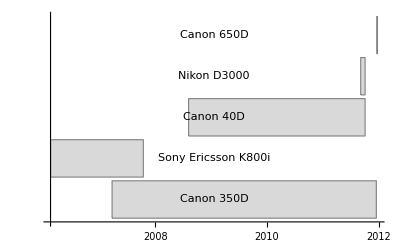

```mathematica
BarChart[{#[[1]]-minCameraTime,#[[2]]-#[[1]],maxCameraTime-#[[2]]}&/@cameraMinMaxTimes,ChartLayout->"Stacked",ChartStyle->{Directive[Transparent,EdgeForm[None]],Directive[LightGray,EdgeForm[Gray]],Directive[Transparent,EdgeForm[None]]},BarOrigin->Left,Axes->{True,False},ChartLabels->{None,Placed[formatLabel/@gatheredCameras,Center],None},Ticks->{yearTickFn,None}]
```

## Aperture

```mathematica
getData[goodFileNames[[1]],"Aperture"]
```

4

```mathematica
imageAperture=Monitor[
Table[getData[goodFileNames[[i]],"Aperture"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

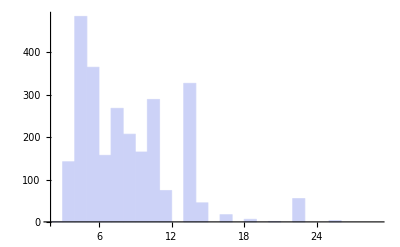

```mathematica
Histogram[imageAperture]
```

```mathematica
Manipulate[Graphics[{EdgeForm[LightGray],Gray,Table[Polygon[{{Cos[t],Sin[t]},{Cos[t-o],Sin[t-o]}/d,{Cos[t+2Pi/6],Sin[t+2Pi/6]},Sequence@@Table[{Cos[x],Sin[x]},{x,t+2Pi/6,t,-0.1}]}],{t,0,2Pi,2Pi/6}]},ImageSize->400],{d,1,10},{o,0,2Pi}]
```

```mathematica
closedAperture=With[{d=4.27,o=0.819513},Graphics[{EdgeForm[LightGray],Gray,Table[Polygon[{{Cos[t],Sin[t]},{Cos[t-o],Sin[t-o]}/d,{Cos[t+(2 π)/6],Sin[t+(2 π)/6]},Sequence@@Table[{Cos[x],Sin[x]},{x,t+(2 π)/6,t,-0.1}]}],{t,0,2 π,(2 π)/6}]},ImageSize->60]]
```

-Graphics-

```mathematica
openAperture=With[{d=1.12,o=0.160796},Graphics[{EdgeForm[LightGray],Gray,Table[Polygon[{{Cos[t],Sin[t]},{Cos[t-o],Sin[t-o]}/d,{Cos[t+(2 π)/6],Sin[t+(2 π)/6]},Sequence@@Table[{Cos[x],Sin[x]},{x,t+(2 π)/6,t,-0.1}]}],{t,0,2 π,(2 π)/6}]},ImageSize->60]]
```

-Graphics-

```mathematica
SmoothHistogram[imageAperture,AxesOrigin->{0,0},Axes->{True,False},PlotRangePadding->{{10,Automatic},Automatic},Filling->Axis,Epilog->{Inset[openAperture,{-3,Center}],Inset[closedAperture,{27,Center}]}]
```

-Graphics-

## Time of day taken

```mathematica
timeOfDayToSeconds[{h_,m_,s_}]:=s+(m+h*60)*60
```

```mathematica
timeOfDayToHour[{h_,m_,s_}]:=h
```

```mathematica
Tally[timeOfDayToHour/@imageDates[[All,4;;]]]
```

{{17,187},{18,196},{22,325},{13,255},{14,252},{15,248},{20,467},{19,183},{23,103},{0,156},{3,30},{4,37},{5,26},{6,23},{12,236},{21,370},{16,193},{1,71},{10,75},{11,183},{8,7},{9,21},{2,31},{7,11}}

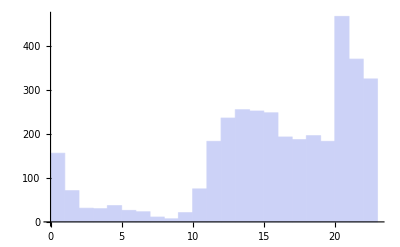

```mathematica
Histogram[timeOfDayToHour/@imageDates[[All,4;;]],Axes->{True,False}]
```

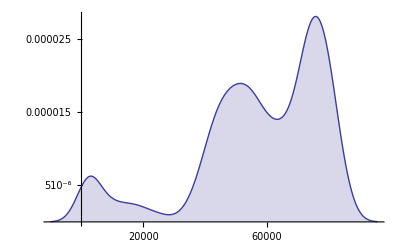

```mathematica
SmoothHistogram[timeOfDayToSeconds/@imageDates[[All,4;;]],Axes->{True,False},Filling->Axis]
```

## Exposure

```mathematica
getData[goodFileNames[[1]],"Exposure"]
```

1/60

```mathematica
imageExposure=Monitor[
Table[getData[goodFileNames[[i]],"Exposure"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Max[imageExposure]
```

139

```mathematica
Min[imageExposure]
```

1/6400

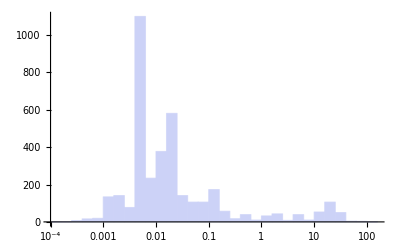

```mathematica
Histogram[imageExposure,"Log",Axes->{True,False}]
```

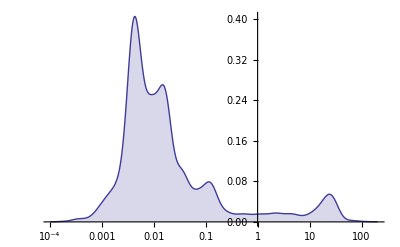

```mathematica
SmoothHistogram[Log@imageExposure,Ticks->{Charting`ScaledTicks[{Log,Exp}],Automatic},Axes->{True,False},Filling->Axis]
```

## Focal length

```mathematica
getData[goodFileNames[[1]],"FocalLength"]
```

28.

```mathematica
imageFocalLength=Monitor[
Table[getData[goodFileNames[[i]],"FocalLength"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Max[imageFocalLength]
```

Max[300.,None]

```mathematica
Min[imageFocalLength]
```

Min[17.,None]

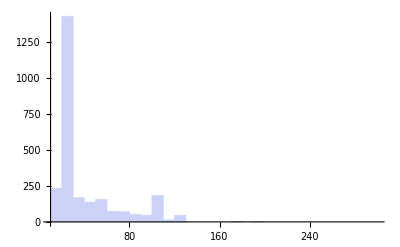

```mathematica
Histogram[imageFocalLength,Axes->{True,False}]
```

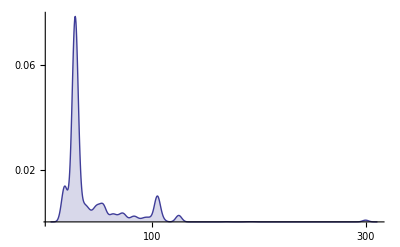

```mathematica
SmoothHistogram[imageFocalLength,Axes->{True,False},Filling->Axis]
```

## Image size

```mathematica
getData[goodFileNames[[1]],"ImageSize"]
```

{3456,2304}

```mathematica
imageSizes=Monitor[
Table[getData[goodFileNames[[i]],"ImageSize"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
talliedImageSizes=Tally[imageSizes];
```

```mathematica
miniTalliesImageSizes=Cases[talliedImageSizes,{{_,_},a_}/;a>1]
```

{{{3456,2304},853},{{2304,3456},516},{{1215,1506},3},{{1506,1215},2},{{3131,1746},2},{{2944,1847},2},{{1689,2261},2},{{2304,1600},2},{{2736,1615},2},{{2241,3362},2},{{2064,3096},2},{{2730,1820},2},{{2215,1477},2},{{2175,1450},2},{{200,200},2},{{2012,1341},2},{{2055,3083},2},{{2021,3031},2},{{1695,2542},2},{{1449,2174},2},{{1536,2304},9},{{2089,3134},4},{{1901,2851},3},{{2812,1874},2},{{2604,1736},2},{{2770,1847},3},{{3036,2024},2},{{2740,1827},2},{{2817,1878},4},{{3242,2161},2},{{2128,3193},2},{{2380,1587},2},{{1826,2739},2},{{3018,2012},2},{{2882,1922},2},{{2515,1677},2},{{3123,2082},2},{{2507,1671},3},{{1947,2920},2},{{3401,2267},2},{{3166,2111},2},{{3374,2249},2},{{2137,1424},2},{{1511,1007},2},{{2483,1656},2},{{3200,2133},2},{{1783,2674},2},{{2048,1536},790},{{3262,2175},3},{{3304,2202},2},{{2224,3336},2},{{2198,3297},2},{{2581,1721},2},{{3280,2186},2},{{1024,683},575},{{1876,2814},2},{{2367,1578},2},{{1680,1120},2},{{2270,1513},2},{{3474,2314},14},{{1861,2791},2},{{2084,3126},2},{{1411,2117},2},{{3311,2208},2},{{1677,2515},2},{{1280,1920},2},{{3256,2171},2},{{2820,1880},2},{{3273,2182},3},{{2077,3115},2},{{3309,2206},2},{{2249,3374},2},{{2093,3140},2},{{3872,2592},34},{{2592,3872},24},{{5184,3456},8},{{3456,5184},3},{{1536,2048},281}}

```mathematica
maxImgSizeNr=Max[talliedImageSizes[[All,2]]]
```

853

```mathematica
Sort[miniTalliesImageSizes,#1[[2]]>#2[[2]]&]
```

{{{3456,2304},853},{{2048,1536},790},{{1024,683},575},{{2304,3456},516},{{1536,2048},281},{{3872,2592},34},{{2592,3872},24},{{3474,2314},14},{{1536,2304},9},{{5184,3456},8},{{2817,1878},4},{{2089,3134},4},{{3456,5184},3},{{3273,2182},3},{{3262,2175},3},{{2507,1671},3},{{2770,1847},3},{{1901,2851},3},{{1215,1506},3},{{2093,3140},2},{{2249,3374},2},{{3309,2206},2},{{2077,3115},2},{{2820,1880},2},{{3256,2171},2},{{1280,1920},2},{{1677,2515},2},{{3311,2208},2},{{1411,2117},2},{{2084,3126},2},{{1861,2791},2},{{2270,1513},2},{{1680,1120},2},{{2367,1578},2},{{1876,2814},2},{{3280,2186},2},{{2581,1721},2},{{2198,3297},2},{{2224,3336},2},{{3304,2202},2},{{1783,2674},2},{{3200,2133},2},{{2483,1656},2},{{1511,1007},2},{{2137,1424},2},{{3374,2249},2},{{3166,2111},2},{{3401,2267},2},{{1947,2920},2},{{3123,2082},2},{{2515,1677},2},{{2882,1922},2},{{3018,2012},2},{{1826,2739},2},{{2380,1587},2},{{2128,3193},2},{{3242,2161},2},{{2740,1827},2},{{3036,2024},2},{{2604,1736},2},{{2812,1874},2},{{1449,2174},2},{{1695,2542},2},{{2021,3031},2},{{2055,3083},2},{{2012,1341},2},{{200,200},2},{{2175,1450},2},{{2215,1477},2},{{2730,1820},2},{{2064,3096},2},{{2241,3362},2},{{2736,1615},2},{{2304,1600},2},{{1689,2261},2},{{2944,1847},2},{{3131,1746},2},{{1506,1215},2}}

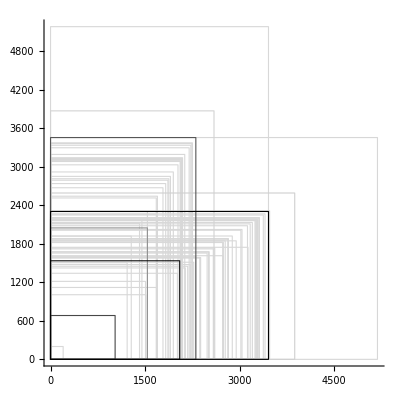

```mathematica
Graphics[{FaceForm[None],EdgeForm[Darker[LightGray,(#[[2]]/maxImgSizeNr)]],Rectangle[{0,0},#[[1]]]}&/@Sort[miniTalliesImageSizes,#1[[2]]<#2[[2]]&],Axes->True,AxesStyle->Gray,AspectRatio->1]
```

Average mexapixel

```mathematica
Mean@N[Times@@@imageSizes/1000000]
```

5.08879

Megapixel distribution

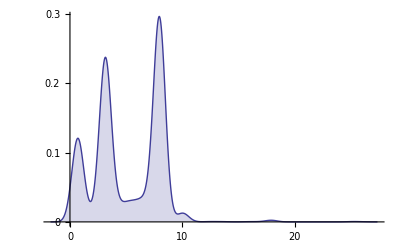

```mathematica
SmoothHistogram[Times@@@imageSizes/1000000,Axes->{True,False},Filling->Axis]
```

## ISO

```mathematica
getData[goodFileNames[[1]],"ISO"]
```

400

```mathematica
imageISO=Monitor[
Table[getData[goodFileNames[[i]],"ISO"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
{labelISO,nrISO}=HistogramList[imageISO,{100}]
```

{{0,100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700},{361,1777,266,7,908,13,52,1,57,0,0,0,0,0,0,0,244}}

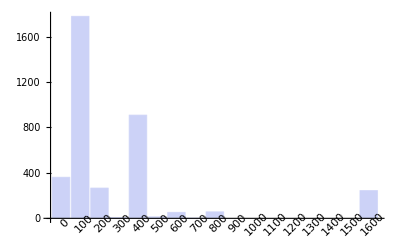

```mathematica
BarChart[nrISO,ChartLabels->Placed[labelISO,Axis,Rotate[#,Pi/4]&],Axes->{True,False}]
```

## Orientations

```mathematica
{orientLabel,orientNr}=Transpose@Tally[If[#[[1]]>#[[2]],"Landscape","Portrait"]&/@imageSizes]
```

{{Landscape,Portrait},{2613,1073}}

```mathematica
{orientLabel,orientNr}=Transpose@Tally[Cases[imageOrientations,Except[None]]]
```

{{Right,Top,Left},{5,1798,9}}

```mathematica
PieChart[orientNr,ChartLabels->Placed[orientLabel/.{"Landscape"->Graphics[{Gray,EdgeForm[Black],Rectangle[{0,0},{3456,2304}]},ImageSize->{60}],"Portrait"->Graphics[{Gray,EdgeForm[Black],Rectangle[{0,0},{2304,3456}]},ImageSize->{60}]},"RadialCenter"]]
```

-Graphics-
-Graphics-

## Image colors over time

```mathematica
ClearAll[getHueValues];
getHueValues[img_]:=Module[{},
Map[Round[First[#],0.02]&,RGBColor@@#&/@Flatten[ImageData[img],1]]
]
```

```mathematica
getHueValues[path_String]:=getHueValues[Import[storageFileImg[path]]]
```

```mathematica
getHueTally[path_]:=getHueTally[path]=Tally@getHueValues[path]
```

```mathematica
getHueCounts[path_]:=Module[{hueVals},
hueVals=getHueValues[path];
Table[Count[hueVals,i],{i,0,1,0.02}]
]
```

```mathematica
getHueCounts[goodFileNames[[2]]]
```

{924,976,735,1115,1426,4032,3171,2476,2364,1888,1873,1798,1954,2430,2426,3021,2396,2647,3571,3296,2568,1812,1019,528,421,483,379,375,389,389,423,481,455,453,468,455,361,309,264,276,240,239,204,193,176,239,160,182,188,301,1051}

```mathematica
dateSortedGoodFileNames=Sort[{#,AbsoluteTime@getData[#,"Date"]}&/@goodFileNames,#1[[2]]<#2[[2]]&][[All,1]];
```

```mathematica
hueCounts=Monitor[
Table[
getHueCounts[dateSortedGoodFileNames[[j]]],{j,Length[dateSortedGoodFileNames]}],
Refresh[
ProgressIndicator[j,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Put[hueCounts,FileNameJoin[{dataDir,"hueCounts.dst"}]]
```

```mathematica
Plus@@Partition[hueCounts,10][[1]]
```

{3146,30410,38294,36300,31920,47262,38298,31989,26730,23525,23672,23350,25689,23203,16003,17313,14214,14734,14997,14251,14115,16219,17576,16996,15278,19538,15467,13668,6338,4145,3986,3729,3621,3567,4084,5827,5295,3183,857,437,384,372,413,456,454,476,419,399,337,541,1523}

```mathematica
partitionedHueCounts=Map[Normalize,Map[Plus@@#&,Partition[hueCounts,40]]];
```

```mathematica
partitionedHueCounts[[1,1]]
```

(1573 √(2/37209561))/15

```mathematica
Length[partitionedHueCounts]
```

368

```mathematica
Length[partitionedHueCounts[[1]]]
```

51

```mathematica
DiscretePlot3D[partitionedHueCounts[[i,j]],{i,1,Length[partitionedHueCounts]},{j,1,Length[partitionedHueCounts[[1]]]},ColorFunction->Function[{x,y,z},Hue[y,0.8]],ExtentSize->Full,PlotStyle->EdgeForm[None],AxesLabel->{"Time","Hue","Count"}]
```

-Graphics3D-

```mathematica
nonTalliedHueValues=Monitor[
Table[
getHueValues[goodFileNames[[j]]],{j,Length[goodFileNames]/10}],
Refresh[
ProgressIndicator[j,{0,Length[goodFileNames]/10}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
hueValues=Monitor[
Table[
getHueTally[goodFileNames[[j]]],{j,Length[goodFileNames]}],
Refresh[
ProgressIndicator[j,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
combineTally[a_,b_]:=Map[{#[[1,1]],Total[#[[All,2]]]}&,GatherBy[Join[a,b],#[[1]]&]]
```

```mathematica
getCombinedTally[values_]:=Module[{hueTally,sortedHueTally},
hueTally=Fold[combineTally,{},hueValues];
sortedHueTally=Sort[hueTally,OrderedQ[{#1[[1]],#2[[1]]}]&]
]
```

```mathematica
getCombinedTally[hueValues]
```

{{0.,4926715},{0.01,2201735},{0.02,3170586},{0.03,2184687},{0.04,3327075},{0.05,3902914},{0.06,2676622},{0.07,3947765},{0.08,2627211},{0.09,3823376},{0.1,2448103},{0.11,3579212},{0.12,2328542},{0.13,3426714},{0.14,2238385},{0.15,3298221},{0.16,3256886},{0.17,2159542},{0.18,3235615},{0.19,2152328},{0.2,3239484},{0.21,2164664},{0.22,3245201},{0.23,2163905},{0.24,3244644},{0.25,3247386},{0.26,2167462},{0.27,3240488},{0.28,2140185},{0.29,3182480},{0.3,2112410},{0.31,3169602},{0.32,2133276},{0.33,3180988},{0.34,2103807},{0.35,3131528},{0.36,3080761},{0.37,2021882},{0.38,2991329},{0.39,1961190},{0.4,2916378},{0.41,1928048},{0.42,2875675},{0.43,1917557},{0.44,2879202},{0.45,2874421},{0.46,1919185},{0.47,2888664},{0.48,1944036},{0.49,2935402},{0.5,1988999},{0.51,2898820},{0.52,1925769},{0.53,2882268},{0.54,1907450},{0.55,2819661},{0.56,2735160},{0.57,1780462},{0.58,2635049},{0.59,1733772},{0.6,2553354},{0.61,1678727},{0.62,2467993},{0.63,1621269},{0.64,2385921},{0.65,2342997},{0.66,1538897},{0.67,2271224},{0.68,1486458},{0.69,2196584},{0.7,1413238},{0.71,2092091},{0.72,1373395},{0.73,2011376},{0.74,1312039},{0.75,1909688},{0.76,1861483},{0.77,1242166},{0.78,1852353},{0.79,1243757},{0.8,1826331},{0.81,1195994},{0.82,1789989},{0.83,1205367},{0.84,1823013},{0.85,1850313},{0.86,1229680},{0.87,1820116},{0.88,1180016},{0.89,1730187},{0.9,1097004},{0.91,1578438},{0.92,1019400},{0.93,1444180},{0.94,878138},{0.95,1171943},{0.96,1049031},{0.97,659534},{0.98,983620},{0.99,670325},{1.,3191187}}

```mathematica
hueValues//Length/1
```

3686

```mathematica
b1=BarChart[Evaluate@{getCombinedTally[#][[All,2]]},ChartLayout->"Percentile",Axes->None,BarSpacing->{0,0},ChartStyle->Map[Hue[#,0.5]&,{getCombinedTally[hueValues][[All,1]]},{2}],ChartBaseStyle->EdgeForm[None],PerformanceGoal->"Speed",ImageSize->{500},AspectRatio->500/10,PlotRangePadding->0,ImagePadding->None]&/@Partition[hueValues,30]
```

$Aborted

```mathematica
MapIndexed[List[#1,#2[[1]]]&,nonTalliedHueValues[[1;;2]],{2}]
```

{{{0.06,1},{0.06,1},{0.06,1},{0.08,1},{0.08,1},{0.06,1},{0.06,1},{0.08,1},{0.08,1},{0.08,1},{0.06,1},{0.06,1},{0.06,1},«59974»,{0.14,1},{0.16,1},{0.16,1},{0.16,1},{0.16,1},{0.16,1},{0.16,1},{0.16,1},{0.16,1},{0.14,1},{0.14,1},{0.14,1},{0.14,1}},«1»}

```mathematica
Join@@@Partition[nonTalliedHueValues[[1;;4]],2]
```

{{0.06,0.06,0.06,0.08,0.08,0.06,0.06,0.08,0.08,0.08,0.06,0.06,0.06,0.06,0.06,0.06,0.08,0.06,0.06,0.06,0.06,0.08,0.08,0.08,0.06,0.08,0.1,0.1,0.08,0.08,0.1,0.12,0.1,0.1,0.1,0.1,0.12,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,«119906»,0.,0.,0.,0.,0.02,0.02,0.02,0.,0.,0.02,0.04,0.08,0.08,0.04,0.06,0.06,0.06,0.06,0.06,0.04,0.04,0.04,0.04,0.06,0.06,0.06,0.04,0.04,0.04,0.04,0.02,0.02,0.04,0.02,0.02,0.04,0.08,0.34,0.24,0.16,0.24,0.34,0.32,0.28,0.1,0.2,0.28},{«1»}}

```mathematica
indexedHues=MapIndexed[List[#1,#2[[1]]]&,Join@@@Partition[nonTalliedHueValues[[1;;40]],10],{2}];
```

```mathematica
HistogramList[indexedHues];
```

HistogramList::hbins: The bin specification Automatic cannot be used to determine either how many or which bins to use.

## Memory used

Total image size in GiB:

```mathematica
N[Total@fileSizes[[All,2]]/1024/1024/1024]
```

5.69425

Mean image size in MiB:

```mathematica
N[Mean[fileSizes[[All,2]]]/1024/1024]
```

1.47431

Max image size in MiB:

```mathematica
N[Max[fileSizes[[All,2]]]/1024/1024]
```

12.254

## Problematic

## Bit depth [boring]

```mathematica
getData[goodFileNames[[1]],"BitDepth"]
```

8

```mathematica
imageBitDepth=Monitor[
Table[getData[goodFileNames[[i]],"BitDepth"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Tally@imageBitDepth
```

{{8,3686}}

## Flash [no data]

## Color space [boring]

```mathematica
getData[goodFileNames[[1]],"ColorSpace"]
```

RGBColor

```mathematica
imageColorSpace=Monitor[
Table[getData[goodFileNames[[i]],"ColorSpace"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Tally@imageColorSpace
```

{{RGBColor,3676},{Grayscale,10}}